```mathematica
SetDirectory[ParentDirectory[ParentDirectory[NotebookDirectory[]]]];
```

## Import Data

```mathematica
Needs["ErrorBarPlots`"];
```

```mathematica
Vdata=SplitBy[Import["latticedata/AllData2p1Flavors/Vall.txt","Table"],First];

ReVdataT[n_]:=Table[Vdata[[n,x,2;;3]],{x,1,Dimensions[Vdata[[n]]][[1]]}];
ImVdataT[n_]:=Table[{Vdata[[n,x,2]],Vdata[[n,x,5]]},{x,1,Dimensions[Vdata[[n]]][[1]]}];
ReVdataTe[n_]:=Table[Vdata[[n,x,2;;4]],{x,1,Dimensions[Vdata[[n]]][[1]]}];
ImVdataTe[n_]:=Table[{Vdata[[n,x,2]],Vdata[[n,x,5]],Vdata[[n,x,6]]},{x,1,Dimensions[Vdata[[n]]][[1]]}];
ReVdataTn[n_]:=ReVdataT[n]/.{a_,b_}:>{a/0.197327,b};
ImVdataTn[n_]:=ImVdataT[n]/.{a_,b_}:>{a/0.197327,b};
ReVdataTne[n_]:=ReVdataTe[n]/.{a_,b_,c_}:>{a/0.197327,b,c};
ImVdataTne[n_]:=ImVdataTe[n]/.{a_,b_,c_}:>{a/0.197327,b,c};

T0data=Join[{Import["latticedata/LowTemp/OlafPotentialLinesTmax12PotentialT41.05.dat","Table"][[All,1;;3]]},{Import["latticedata/LowTemp/OlafPotentialLinesTmax12PotentialT71.54.dat","Table"][[All,1;;3]]}];
T0datan=T0data/.{a_,b_,c_}:>{a/0.197327,b,c};
```

## Define functions for real part

```mathematica
ReV[r_,m_,α_,σ_,c_]:=-α m-α Exp[-m r]/r-Gamma[1/4]/(2^(3/4)√π)σ/((m^2 σ/α)^(1/4))ParabolicCylinderD[-1/2,√2(m^2 σ/α)^(1/4) r]+Gamma[1/4]/(2Gamma[3/4])σ/((m^2 σ/α)^(1/4))+c

ReVsb[r_,m_,α_,σ_,c_]:=If[ReV[r,m,α,σ,c]<ReVsbVac,ReV[r,m,α,σ,c],ReVsbVac];
```

```mathematica
N[Limit[ReV[r,m,α,σ,c],m->0]]//Simplify
```

c-(1. α)/r+1. r σ

```mathematica
ReVm0[r_,α_,σ_,c_]:=c-α/r+σ r;
```

```mathematica
ReVm0sb[r_,α_,σ_,c_]:=Piecewise[{{c-α/r+σ r,r<rsb},{c-α/r+σ rsb,r≥rsb}}]
```

```mathematica
rsb=6.145111521103572;
```

```mathematica
ParallelSow[exp_,tag_]:=Sow[exp,tag];
SetSharedFunction[ParallelSow];
```

## Low T Cornell Fitting & Interpolation

```mathematica
T0datarand[n_]:=Table[{T0datan[[n]][[i,1]],RandomVariate[NormalDistribution[T0data[[n]][[i,2]],T0data[[n]][[i,3]]]]},{i,Length[T0data[[n]]]}]
```

### beta = 6.9 Fitting

```mathematica
VaryFitLow=Range[2,4];
VaryFitHigh=Range[20,28];
VaryFit=Flatten[Table[{VaryFitLow[[j]],VaryFitHigh[[i]]},{j,1,Length[VaryFitLow]},{i,1,Length[VaryFitHigh]}],1];

VaryFitLowAR={2,2,2,2,2,1,3,1,3}+1;
VaryFitHighAR={24,28,26,30,22,24,24,26,22}-2;
```

#### Varied Weights (not in use)

{0.449955,0.0207984}

{0.223087,0.00686867}

{1.75543,0.0257048}

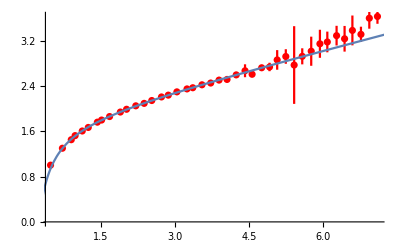

```mathematica
αfit69={};
σfit69={};
cfit69={};
Do[Module[{fit},fit=NonlinearModelFit[T0data[[1,All,1;;2]][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{al,sig,const},r,Weights->1/(T0data[[1,All,3]][[VaryFit[[i,1]];;VaryFit[[i,2]]]])];
αfit69=Append[αfit69,al/.fit["BestFitParameters"]];
σfit69=Append[σfit69,sig/.fit["BestFitParameters"]];
cfit69=Append[cfit69,const/.fit["BestFitParameters"]]];,{i,1,Length[VaryFit]}]
αfinal69={Mean[αfit69],StandardDeviation[αfit69]}
σfinal69={Mean[σfit69],StandardDeviation[σfit69]}
cfinal69={Mean[cfit69],StandardDeviation[cfit69]}
Show[{ErrorListPlot[T0data[[1,All]],PlotStyle->{Red},PlotRange->All],Plot[ReVm0[r,αfinal69[[1]],σfinal69[[1]],cfinal69[[1]]],{r,0,10}]}]
```

{0.437304,0.0639055}

{0.230147,0.0267482}

{1.7356,0.088547}

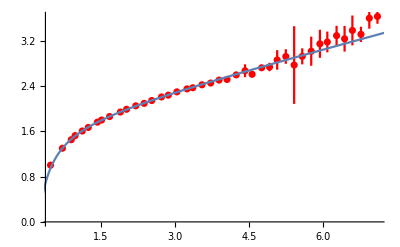

```mathematica
αfit69={};
σfit69={};
cfit69={};
Do[Module[{fit},fit=NonlinearModelFit[T0data[[1,All,1;;2]][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{al,sig,const},r,Weights->1/(T0data[[1,All,3]][[VaryFit[[i,1]];;VaryFit[[i,2]]]])^2];
αfit69=Append[αfit69,al/.fit["BestFitParameters"]];
σfit69=Append[σfit69,sig/.fit["BestFitParameters"]];
cfit69=Append[cfit69,const/.fit["BestFitParameters"]]];,{i,1,Length[VaryFit]}]
αfinal69={Mean[αfit69],StandardDeviation[αfit69]}
σfinal69={Mean[σfit69],StandardDeviation[σfit69]}
cfinal69={Mean[cfit69],StandardDeviation[cfit69]}
Show[{ErrorListPlot[T0data[[1,All]],PlotStyle->{Red},PlotRange->All],Plot[ReVm0[r,αfinal69[[1]],σfinal69[[1]],cfinal69[[1]]],{r,0,10}]}]
```

```mathematica
αfit69={};
σfit69={};
cfit69={};
Do[Module[{fit},fit=NonlinearModelFit[T0data[[1,All,1;;2]][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{al,sig,const},r,Weights->1/(T0data[[1,All,3]][[VaryFit[[i,1]];;VaryFit[[i,2]]]]),VarianceEstimatorFunction->(1&)];
αfit69=Append[αfit69,al/.fit["BestFitParameters"]];
σfit69=Append[σfit69,sig/.fit["BestFitParameters"]];
cfit69=Append[cfit69,const/.fit["BestFitParameters"]]];,{i,1,Length[VaryFit]}]
αfinal69={Mean[αfit69],StandardDeviation[αfit69]}
σfinal69={Mean[σfit69],StandardDeviation[σfit69]}
cfinal69={Mean[cfit69],StandardDeviation[cfit69]}
Show[{ErrorListPlot[T0data[[1,All]],PlotStyle->{Red},PlotRange->All],Plot[ReVm0[r,αfinal69[[1]],σfinal69[[1]],cfinal69[[1]]],{r,0,10}]}]
```

{0.449955,0.0207984}

{0.223087,0.00686867}

{1.75543,0.0257048}

-Graphics-

```mathematica
αfit69={};
σfit69={};
cfit69={};
Do[Module[{fit},fit=NonlinearModelFit[T0data[[1,All,1;;2]][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{al,sig,const},r,Weights->1/(T0data[[1,All,3]][[VaryFit[[i,1]];;VaryFit[[i,2]]]])^2,VarianceEstimatorFunction->(1&)];
αfit69=Append[αfit69,al/.fit["BestFitParameters"]];
σfit69=Append[σfit69,sig/.fit["BestFitParameters"]];
cfit69=Append[cfit69,const/.fit["BestFitParameters"]]];,{i,1,Length[VaryFit]}]
αfinal69={Mean[αfit69],StandardDeviation[αfit69]}
σfinal69={Mean[σfit69],StandardDeviation[σfit69]}
cfinal69={Mean[cfit69],StandardDeviation[cfit69]}
Show[{ErrorListPlot[T0data[[1,All]],PlotStyle->{Red},PlotRange->All],Plot[ReVm0[r,αfinal69[[1]],σfinal69[[1]],cfinal69[[1]]],{r,0,10}]}]
```

{0.437304,0.0639055}

{0.230147,0.0267482}

{1.7356,0.088547}

-Graphics-

#### Use this one!

```mathematica
res=Reap[Parallelize[Do[Block[{fit0,fit,al0,sig0,const0,al,sig,const},fit0=NonlinearModelFit[T0datarand[1][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{al,sig,const},r];
al0=al/.fit0["BestFitParameters"];
sig0=sig/.fit0["BestFitParameters"];
const0=const/.fit0["BestFitParameters"];fit=NonlinearModelFit[T0datarand[1][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{{al,al0},{sig,sig0},{const,const0}},r];
ParallelSow[al/.fit["BestFitParameters"],a];
ParallelSow[sig/.fit["BestFitParameters"],s];
ParallelSow[const/.fit["BestFitParameters"],c];],{ii,1,10000},{i,1,Length[VaryFit]}]],{a,s,c}];//AbsoluteTiming
αfinal69r={Mean[res[[2,1,1]]],StandardDeviation[res[[2,1,1]]]}
σfinal69r={Mean[res[[2,2,1]]],StandardDeviation[res[[2,2,1]]]}
cfinal69r={Mean[res[[2,3,1]]],StandardDeviation[res[[2,3,1]]]}
Clear[res];
```

```mathematica
αfinal69r={0.4710450069837839,0.04702624722849975};(*10k run*)
σfinal69r={0.21706585496978312,0.01591666832848482};
cfinal69r={1.7808011444056948,0.05933918615308069};
```

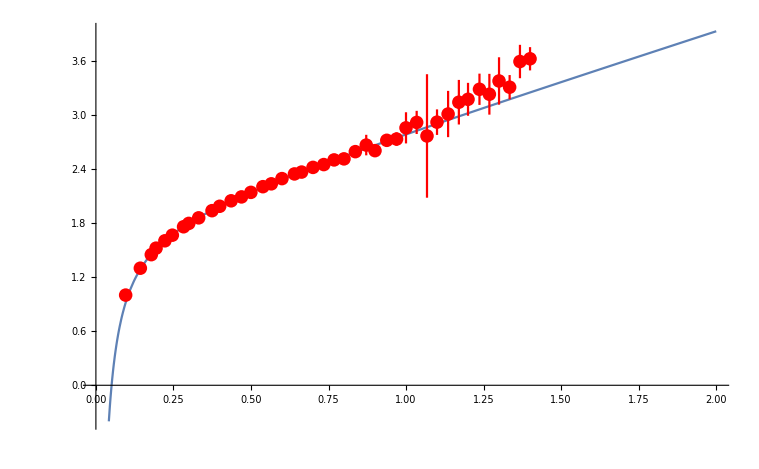

```mathematica
Show[{Plot[ReVm0[r/0.197327,αfinal69r[[1]],σfinal69r[[1]],cfinal69r[[1]]],{r,0,2}],ErrorListPlot[T0data[[1,All]],PlotStyle->{Red},PlotRange->All]}]
```

### beta = 7.4 Fitting

```mathematica
VaryFitLow=Range[5,7];
VaryFitHigh=Range[26,34];
VaryFit=Flatten[Table[{VaryFitLow[[j]],VaryFitHigh[[i]]},{j,1,Length[VaryFitLow]},{i,1,Length[VaryFitHigh]}],1];
```

```mathematica
VaryFitLowAR={2,2,2,2,2,1,3,1,3}+4;
VaryFitHighAR={24,28,26,30,22,24,24,26,22}+4;
```

#### Varied Weights (not in use)

{0.386026,0.00681763}

{0.264172,0.003189}

{2.65021,0.00972345}

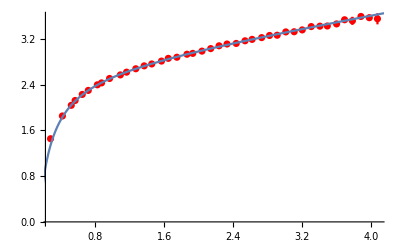

```mathematica
αfit748={};
σfit748={};
cfit748={};
Do[Module[{fit},fit=NonlinearModelFit[T0data[[2,All,1;;2]][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{al,sig,const},r,Weights->1/(T0data[[2,All,3]][[VaryFit[[i,1]];;VaryFit[[i,2]]]])];
αfit748=Append[αfit748,al/.fit["BestFitParameters"]];
σfit748=Append[σfit748,sig/.fit["BestFitParameters"]];
cfit748=Append[cfit748,const/.fit["BestFitParameters"]]];,{i,1,Length[VaryFit]}]
αfinal748={Mean[αfit748],StandardDeviation[αfit748]}
σfinal748={Mean[σfit748],StandardDeviation[σfit748]}
cfinal748={Mean[cfit748],StandardDeviation[cfit748]}
Show[{ErrorListPlot[T0data[[2,All]],PlotStyle->{Red},PlotRange->All],Plot[ReVm0[r,αfinal748[[1]],σfinal748[[1]],cfinal748[[1]]],{r,0,10}]}]
```

{0.389033,0.00967473}

{0.263519,0.00430806}

{2.65451,0.0135868}

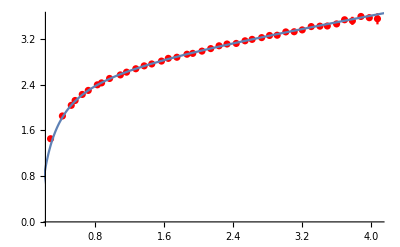

```mathematica
αfit748={};
σfit748={};
cfit748={};
Do[Module[{fit},fit=NonlinearModelFit[T0data[[2,All,1;;2]][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{al,sig,const},r,Weights->1/(T0data[[2,All,3]][[VaryFit[[i,1]];;VaryFit[[i,2]]]])^2];
αfit748=Append[αfit748,al/.fit["BestFitParameters"]];
σfit748=Append[σfit748,sig/.fit["BestFitParameters"]];
cfit748=Append[cfit748,const/.fit["BestFitParameters"]]];,{i,1,Length[VaryFit]}]
αfinal748={Mean[αfit748],StandardDeviation[αfit748]}
σfinal748={Mean[σfit748],StandardDeviation[σfit748]}
cfinal748={Mean[cfit748],StandardDeviation[cfit748]}
Show[{ErrorListPlot[T0data[[2,All]],PlotStyle->{Red},PlotRange->All],Plot[ReVm0[r,αfinal748[[1]],σfinal748[[1]],cfinal748[[1]]],{r,0,10}]}]
```

```mathematica
αfit748={};
σfit748={};
cfit748={};
Do[Module[{fit},fit=NonlinearModelFit[T0data[[2,All,1;;2]][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{al,sig,const},r,Weights->1/(T0data[[2,All,3]][[VaryFit[[i,1]];;VaryFit[[i,2]]]]),VarianceEstimatorFunction->(1&)];
αfit748=Append[αfit748,al/.fit["BestFitParameters"]];
σfit748=Append[σfit748,sig/.fit["BestFitParameters"]];
cfit748=Append[cfit748,const/.fit["BestFitParameters"]]];,{i,1,Length[VaryFit]}]
αfinal748={Mean[αfit748],StandardDeviation[αfit748]}
σfinal748={Mean[σfit748],StandardDeviation[σfit748]}
cfinal748={Mean[cfit748],StandardDeviation[cfit748]}
Show[{ErrorListPlot[T0data[[2,All]],PlotStyle->{Red},PlotRange->All],Plot[ReVm0[r,αfinal748[[1]],σfinal748[[1]],cfinal748[[1]]],{r,0,10}]}]
```

{0.386026,0.00681763}

{0.264172,0.003189}

{2.65021,0.00972345}

-Graphics-

```mathematica
αfit748={};
σfit748={};
cfit748={};
Do[Module[{fit},fit=NonlinearModelFit[T0data[[2,All,1;;2]][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{al,sig,const},r,Weights->1/(T0data[[2,All,3]][[VaryFit[[i,1]];;VaryFit[[i,2]]]])^2,VarianceEstimatorFunction->(1&)];
αfit748=Append[αfit748,al/.fit["BestFitParameters"]];
σfit748=Append[σfit748,sig/.fit["BestFitParameters"]];
cfit748=Append[cfit748,const/.fit["BestFitParameters"]]];,{i,1,Length[VaryFit]}]
αfinal748={Mean[αfit748],StandardDeviation[αfit748]}
σfinal748={Mean[σfit748],StandardDeviation[σfit748]}
cfinal748={Mean[cfit748],StandardDeviation[cfit748]}
Show[{ErrorListPlot[T0data[[2,All]],PlotStyle->{Red},PlotRange->All],Plot[ReVm0[r,αfinal748[[1]],σfinal748[[1]],cfinal748[[1]]],{r,0,10}]}]
```

{0.389033,0.00967473}

{0.263519,0.00430806}

{2.65451,0.0135868}

-Graphics-

#### Use this one!

```mathematica
ParallelSow[exp_,tag_]:=Sow[exp,tag];
SetSharedFunction[ParallelSow];
```

```mathematica
res=Reap[Parallelize[Do[Block[{fit0,fit,al0,sig0,const0,al,sig,const},fit0=NonlinearModelFit[T0datarand[2][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{al,sig,const},r];
al0=al/.fit0["BestFitParameters"];
sig0=sig/.fit0["BestFitParameters"];
const0=const/.fit0["BestFitParameters"];fit=NonlinearModelFit[T0datarand[2][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{{al,al0},{sig,sig0},{const,const0}},r];
ParallelSow[al/.fit["BestFitParameters"],a];
ParallelSow[sig/.fit["BestFitParameters"],s];
ParallelSow[const/.fit["BestFitParameters"],c];],{ii,1,10000},{i,1,Length[VaryFit]}]],{a,s,c}];//AbsoluteTiming
αfinal748r={Mean[res[[2,1,1]]],StandardDeviation[res[[2,1,1]]]}
σfinal748r={Mean[res[[2,2,1]]],StandardDeviation[res[[2,2,1]]]}
cfinal748r={Mean[res[[2,3,1]]],StandardDeviation[res[[2,3,1]]]}
Clear[res];
```

```mathematica
αfinal748r={0.3845423173281533,0.02687776218374673};(*10k run*)
σfinal748r={0.2647558584856831,0.014386586309071796};
cfinal748r={2.647529288961358,0.04204617641275159};
```

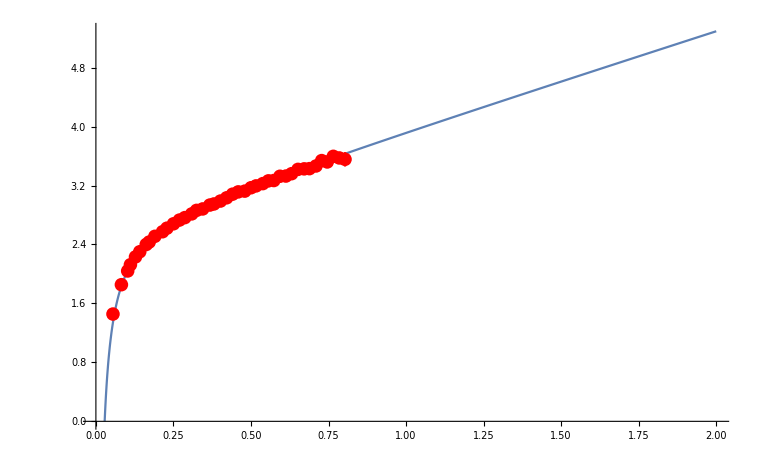

```mathematica
Show[{Plot[ReVm0[r/0.197327,αfinal748r[[1]],σfinal748r[[1]],cfinal748r[[1]]],{r,0,2}],ErrorListPlot[T0data[[2,All]],PlotStyle->{Red},PlotRange->All]}]
```

### Linear Interpolation

```mathematica
β={6.8,6.9,7,7.125,7.25,7.3,7.48};
T={0.1478,0.1642,0.1818,0.2054,0.2317,0.2425,0.2861};
```

```mathematica
btinter=Interpolation[Transpose[{T,β}]];
btinter1=Interpolation[Transpose[{T,β}],InterpolationOrder->1];
```

```mathematica
beta2T0res={αfinal69r,σfinal69r,cfinal69r};
beta7T0res={αfinal748r,σfinal748r,cfinal748r};
```

```mathematica
T0constfit={LinearModelFit[{{β[[2]],beta2T0res[[1,1]]},{β[[7]],beta7T0res[[1,1]]}},x,x],LinearModelFit[{{β[[2]],beta2T0res[[2,1]]},{β[[7]],beta7T0res[[2,1]]}},x,x],LinearModelFit[{{β[[2]],beta2T0res[[3,1]]},{β[[7]],beta7T0res[[3,1]]}},x,x]};
T0errfit={LinearModelFit[{{β[[2]],beta2T0res[[1,2]]},{β[[7]],beta7T0res[[1,2]]}},x,x],LinearModelFit[{{β[[2]],beta2T0res[[2,2]]},{β[[7]],beta7T0res[[2,2]]}},x,x],LinearModelFit[{{β[[2]],beta2T0res[[3,2]]},{β[[7]],beta7T0res[[3,2]]}},x,x]};
```

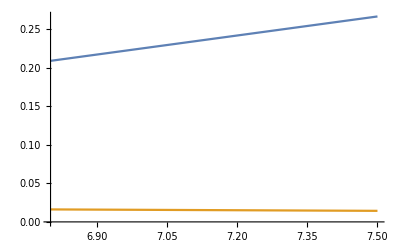

```mathematica
Plot[{T0constfit[[2]][x],T0errfit[[2]][x]},{x,6.8,7.5}]
```

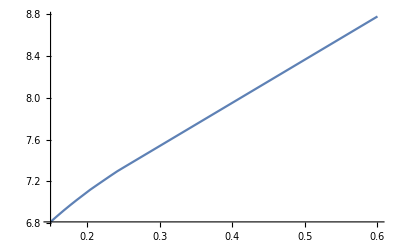

```mathematica
Plot[btinter1[x],{x,0.15,0.6}]
```

```mathematica
Table[T0constfit[[3]][β[[i]]],{i,1,Length[β]}]
```

{1.63137,1.7808,1.93024,2.11703,2.30383,2.37854,2.64753}

```mathematica
Table[T0errfit[[2]][β[[i]]],{i,1,Length[β]}]
```

{0.0161805,0.0159167,0.0156529,0.0153231,0.0149933,0.0148614,0.0143866}

```mathematica
Tscanc=Table[i,{i,0.15,0.25,0.003}]
```

{0.15,0.153,0.156,0.159,0.162,0.165,0.168,0.171,0.174,0.177,0.18,0.183,0.186,0.189,0.192,0.195,0.198,0.201,0.204,0.207,0.21,0.213,0.216,0.219,0.222,0.225,0.228,0.231,0.234,0.237,0.24,0.243,0.246,0.249}

```mathematica
Tscanb=Table[i,{i,0.15,0.6,0.005}]
```

{0.15,0.155,0.16,0.165,0.17,0.175,0.18,0.185,0.19,0.195,0.2,0.205,0.21,0.215,0.22,0.225,0.23,0.235,0.24,0.245,0.25,0.255,0.26,0.265,0.27,0.275,0.28,0.285,0.29,0.295,0.3,0.305,0.31,0.315,0.32,0.325,0.33,0.335,0.34,0.345,0.35,0.355,0.36,0.365,0.37,0.375,0.38,0.385,0.39,0.395,0.4,0.405,0.41,0.415,0.42,0.425,0.43,0.435,0.44,0.445,0.45,0.455,0.46,0.465,0.47,0.475,0.48,0.485,0.49,0.495,0.5,0.505,0.51,0.515,0.52,0.525,0.53,0.535,0.54,0.545,0.55,0.555,0.56,0.565,0.57,0.575,0.58,0.585,0.59,0.595,0.6}

```mathematica
βTscanc=Table[btinter[i],{i,0.15,0.25,0.003}]
```

{6.81385,6.8325,6.85091,6.86907,6.887,6.9047,6.92218,6.93945,6.95652,6.97339,6.99007,7.00662,7.02305,7.03931,7.05539,7.0713,7.08702,7.10256,7.1179,7.13291,7.1476,7.16212,7.17648,7.19072,7.20484,7.21888,7.23284,7.24676,7.26075,7.2747,7.28855,7.30228,7.31589,7.32936}

```mathematica
βTscanc1=Table[btinter1[i],{i,0.15,0.25,0.003}]
```

{6.81341,6.83171,6.85,6.86829,6.88659,6.90455,6.92159,6.93864,6.95568,6.97273,6.98977,7.00636,7.02225,7.03814,7.05403,7.06992,7.08581,7.10169,7.11758,7.1326,7.14686,7.16112,7.17538,7.18964,7.2039,7.21816,7.23241,7.24667,7.26065,7.27454,7.28843,7.30206,7.31445,7.32683}

```mathematica
βTscanb=Join[Table[btinter[i],{i,0.15,0.285,0.005}],Table[btinter1[i],{i,0.29,0.6,0.005}]]
```

InterpolatingFunction::dmval: Input value {0.29} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.295} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.3} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{6.81385,6.8448,6.87507,6.9047,6.93372,6.96216,6.99007,7.01759,7.04469,7.0713,7.0974,7.12298,7.1476,7.17171,7.19544,7.21888,7.24212,7.26541,7.28855,7.31137,7.33382,7.35585,7.3774,7.39842,7.41885,7.43864,7.45773,7.47607,7.4961,7.51674,7.53739,7.55803,7.57867,7.59931,7.61995,7.6406,7.66124,7.68188,7.70252,7.72317,7.74381,7.76445,7.78509,7.80573,7.82638,7.84702,7.86766,7.8883,7.90894,7.92959,7.95023,7.97087,7.99151,8.01216,8.0328,8.05344,8.07408,8.09472,8.11537,8.13601,8.15665,8.17729,8.19794,8.21858,8.23922,8.25986,8.2805,8.30115,8.32179,8.34243,8.36307,8.38372,8.40436,8.425,8.44564,8.46628,8.48693,8.50757,8.52821,8.54885,8.5695,8.59014,8.61078,8.63142,8.65206,8.67271,8.69335,8.71399,8.73463,8.75528,8.77592}

```mathematica
βTscanb1=Table[btinter1[i],{i,0.15,0.6,0.005}]
```

InterpolatingFunction::dmval: Input value {0.29} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.295} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.3} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{6.81341,6.8439,6.87439,6.90455,6.93295,6.96136,6.98977,7.01695,7.04343,7.06992,7.0964,7.12288,7.14686,7.17063,7.19439,7.21816,7.24192,7.26528,7.28843,7.31032,7.33096,7.35161,7.37225,7.39289,7.41353,7.43417,7.45482,7.47546,7.4961,7.51674,7.53739,7.55803,7.57867,7.59931,7.61995,7.6406,7.66124,7.68188,7.70252,7.72317,7.74381,7.76445,7.78509,7.80573,7.82638,7.84702,7.86766,7.8883,7.90894,7.92959,7.95023,7.97087,7.99151,8.01216,8.0328,8.05344,8.07408,8.09472,8.11537,8.13601,8.15665,8.17729,8.19794,8.21858,8.23922,8.25986,8.2805,8.30115,8.32179,8.34243,8.36307,8.38372,8.40436,8.425,8.44564,8.46628,8.48693,8.50757,8.52821,8.54885,8.5695,8.59014,8.61078,8.63142,8.65206,8.67271,8.69335,8.71399,8.73463,8.75528,8.77592}

```mathematica
Table[T0constfit[[2]][βTscanc[[i]]],{i,1,Length[βTscanc]}]
```

{0.209982,0.211516,0.213029,0.214523,0.215997,0.217452,0.21889,0.22031,0.221713,0.2231,0.224472,0.225832,0.227183,0.22852,0.229843,0.23115,0.232443,0.233721,0.234983,0.236217,0.237425,0.238618,0.239799,0.24097,0.242131,0.243285,0.244434,0.245578,0.246729,0.247875,0.249014,0.250143,0.251262,0.25237}

```mathematica
Table[T0constfit[[1]][βTscanc[[i]]],{i,1,Length[βTscanc]}]
```

{0.483894,0.481112,0.478367,0.475658,0.472984,0.470344,0.467737,0.465161,0.462616,0.4601,0.457611,0.455144,0.452693,0.450268,0.44787,0.445498,0.443153,0.440835,0.438546,0.436308,0.434117,0.431952,0.42981,0.427686,0.42558,0.423487,0.421404,0.419329,0.417241,0.415161,0.413096,0.411048,0.409018,0.407009}

```mathematica
Table[T0constfit[[3]][βTscanc[[i]]],{i,1,Length[βTscanc]}]
```

{1.65206,1.67994,1.70744,1.73458,1.76137,1.78782,1.81394,1.83975,1.86526,1.89047,1.91541,1.94013,1.96468,1.98898,2.01301,2.03678,2.06027,2.08349,2.10643,2.12885,2.1508,2.1725,2.19397,2.21524,2.23635,2.25732,2.27819,2.29898,2.3199,2.34074,2.36143,2.38195,2.40229,2.42242}

```mathematica
Table[T0constfit[[2]][βTscanb[[i]]],{i,1,Length[βTscanb]}]
```

{0.209982,0.212527,0.215016,0.217452,0.219838,0.222177,0.224472,0.226735,0.228963,0.23115,0.233297,0.2354,0.237425,0.239407,0.241358,0.243285,0.245197,0.247112,0.249014,0.25089,0.252736,0.254548,0.25632,0.258048,0.259728,0.261355,0.262925,0.264433,0.26608,0.267777,0.269474,0.271172,0.272869,0.274566,0.276263,0.277961,0.279658,0.281355,0.283053,0.28475,0.286447,0.288144,0.289842,0.291539,0.293236,0.294934,0.296631,0.298328,0.300025,0.301723,0.30342,0.305117,0.306815,0.308512,0.310209,0.311907,0.313604,0.315301,0.316998,0.318696,0.320393,0.32209,0.323788,0.325485,0.327182,0.328879,0.330577,0.332274,0.333971,0.335669,0.337366,0.339063,0.34076,0.342458,0.344155,0.345852,0.34755,0.349247,0.350944,0.352641,0.354339,0.356036,0.357733,0.359431,0.361128,0.362825,0.364522,0.36622,0.367917,0.369614,0.371312}

```mathematica
Table[T0constfit[[1]][βTscanb[[i]]],{i,1,Length[βTscanb]}]
```

{0.483894,0.479278,0.474763,0.470344,0.466017,0.461774,0.457611,0.453507,0.449466,0.445498,0.441605,0.43779,0.434117,0.430521,0.426983,0.423487,0.42002,0.416546,0.413096,0.409693,0.406344,0.403059,0.399844,0.39671,0.393663,0.390711,0.387864,0.385128,0.382141,0.379062,0.375984,0.372905,0.369826,0.366748,0.363669,0.360591,0.357512,0.354433,0.351355,0.348276,0.345197,0.342119,0.33904,0.335962,0.332883,0.329804,0.326726,0.323647,0.320568,0.31749,0.314411,0.311332,0.308254,0.305175,0.302097,0.299018,0.295939,0.292861,0.289782,0.286703,0.283625,0.280546,0.277468,0.274389,0.27131,0.268232,0.265153,0.262074,0.258996,0.255917,0.252838,0.24976,0.246681,0.243603,0.240524,0.237445,0.234367,0.231288,0.228209,0.225131,0.222052,0.218974,0.215895,0.212816,0.209738,0.206659,0.20358,0.200502,0.197423,0.194344,0.191266}

```mathematica
Table[T0constfit[[3]][βTscanb[[i]]],{i,1,Length[βTscanb]}]
```

{1.65206,1.69831,1.74355,1.78782,1.83118,1.87369,1.91541,1.95652,1.99702,2.03678,2.07578,2.11401,2.1508,2.18683,2.22229,2.25732,2.29206,2.32686,2.36143,2.39553,2.42908,2.462,2.49421,2.52562,2.55615,2.58572,2.61425,2.64166,2.67159,2.70244,2.73328,2.76413,2.79498,2.82582,2.85667,2.88752,2.91836,2.94921,2.98006,3.01091,3.04175,3.0726,3.10345,3.13429,3.16514,3.19599,3.22683,3.25768,3.28853,3.31937,3.35022,3.38107,3.41191,3.44276,3.47361,3.50445,3.5353,3.56615,3.597,3.62784,3.65869,3.68954,3.72038,3.75123,3.78208,3.81292,3.84377,3.87462,3.90546,3.93631,3.96716,3.998,4.02885,4.0597,4.09055,4.12139,4.15224,4.18309,4.21393,4.24478,4.27563,4.30647,4.33732,4.36817,4.39901,4.42986,4.46071,4.49155,4.5224,4.55325,4.58409}

## Debye Fitting

```mathematica
ReVdataTnrand[n_]:=Table[{ReVdataTne[n][[i,1]],RandomVariate[NormalDistribution[ReVdataTne[n][[i,2]],ReVdataTne[n][[i,3]]]]},{i,Length[ReVdataTne[n]]}]
```

```mathematica
T0constrand[n_]:={RandomVariate[NormalDistribution[T0constfit[[1]][β[[n]]],T0errfit[[1]][β[[n]]]]],RandomVariate[NormalDistribution[T0constfit[[2]][β[[n]]],T0errfit[[2]][β[[n]]]]],RandomVariate[NormalDistribution[T0constfit[[3]][β[[n]]],T0errfit[[3]][β[[n]]]]]}
```

```mathematica
VaryFitLow=Range[1,3];
VaryFitHigh=Range[18,30];
VaryFit=Flatten[Table[{VaryFitLow[[j]],VaryFitHigh[[i]]},{j,1,Length[VaryFitLow]},{i,1,Length[VaryFitHigh]}],1];
VaryFitLow={2,2,2,2,2,1,3,1,3};
VaryFitHigh={32,28,26,24,20,22,22,30,30}-2;
```

```mathematica
mdfitrand[n_,runs_]:=Block[{res},res=Reap[ParallelDo[ParallelSow[Quiet[m/.NonlinearModelFit[ReVdataTnrand[n][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReV[r,m,T0constrand[n][[1]],T0constrand[n][[2]],T0constrand[n][[3]]],{{m,0.1}},r]["BestFitParameters"]],m],{ii,1,runs},{i,1,Length[VaryFit]}],m];
Return[{Mean[res[[2,1]]],StandardDeviation[res[[2,1]]]}]]
```

```mathematica
mdfitrandfinal=ConstantArray[0,Length[Vdata]];
```

```mathematica
mdfitrandfinal[[1]]=mdfitrand[1,10000]//AbsoluteTiming
```

{5213.43,{0.0387961,0.0673575}}

```mathematica
mdfitrandfinal[[2]]=mdfitrand[2,10000]
```

{0.125691,0.109042}

```mathematica
mdfitrandfinal[[3]]=mdfitrand[3,10000]
```

{0.188868,0.128543}

```mathematica
mdfitrandfinal[[4]]=mdfitrand[4,10000]
```

{0.373492,0.18144}

```mathematica
mdfitrandfinal[[5]]=mdfitrand[5,10000]
```

{0.480462,0.148436}

```mathematica
mdfitrandfinal[[6]]=mdfitrand[6,10000]
```

{0.496706,0.179715}

```mathematica
mdfitrandfinal[[7]]=mdfitrand[7,10000]
```

{0.667653,0.175855}

```mathematica
mdfitrandfinal={{0.06997549222118046,0.1037115242744302},{0.18764366844838265,0.14028620574484613},{0.25469933582761983,0.15037687171606728},{0.3734921779850663,0.1814400917223719},{0.5267111789784007,0.14826454016753024},{0.5405169214400376,0.16873718654345912},{0.6676534051261366,0.17585549294099578}};(*10k run*)
```

## Plotting of imaginary part

```mathematica
(*Vsk[k_,rsb_,σ_]:=4π σ((-2+(2-k^2 rsb^2) Cos[k rsb]+2 k rsb Sin[k rsb])/k^4+rsb(k rsb Cos[k rsb]-Sin[k rsb])/k^3)*)
```

```mathematica
(*Imϵk[k_,mD_,T_]:=-π T(k mD^2)/((k^2+mD^2)^2);*)
```

```mathematica
(*(4π)/(2π)^3 k^2 Sinc[k r]Imϵk[k,mD,T]Vsk[k,rsb,σ]//FullSimplify*)
```

```mathematica
(*ImVsI[r_,rsb_,mD_,α_,σ_,T_]:=Block[{norm=NIntegrate[(2 mD^2 T σ (-2+2 Cos[k rsb]+k rsb Sin[k rsb]))/(k (k^2+mD^2)^2),{k,0,∞}]},NIntegrate[(2 mD^2 T σ (-2+2 Cos[k rsb]+k rsb Sin[k rsb]) Sinc[k r])/(k (k^2+mD^2)^2),{k,0,∞}]-norm+T α (1-1/2 √π MeijerG[{{0},{}},{{0,1},{-1/2}},(mD^2 r^2)/4])];*)
```

```mathematica
ImVc[r_,mD_,α_,T_]:=T α (1-1/2 √π MeijerG[{{0},{}},{{0,1},{-1/2}},(mD^2 r^2)/4]);
```

```mathematica
ImVs[r_,mD_,σ_,T_]:=1/4 mD √π r^3 T σ MeijerG[{{-1/2,-1/2},{}},{{1/2,1/2},{-3/2,-1}},(mD^2 r^2)/4];
```

```mathematica
ImV[r_,mD_,α_,σ_,T_]:=(T α (1-1/2 √π MeijerG[{{0},{}},{{0,1},{-1/2}},(mD^2 r^2)/4])+1/4 mD √π r^3 T σ MeijerG[{{-1/2,-1/2},{}},{{1/2,1/2},{-3/2,-1}},(mD^2 r^2)/4]);
```

```mathematica
ImVsb[r_,mD_,α_,σ_,T_]:=Piecewise[{{T α (1-1/2 √π MeijerG[{{0},{}},{{0,1},{-1/2}},(mD^2 r^2)/4])+1/4 mD √π r^3 T σ MeijerG[{{-1/2,-1/2},{}},{{1/2,1/2},{-3/2,-1}},(mD^2 r^2)/4],r<rsb},{T α (1-1/2 √π MeijerG[{{0},{}},{{0,1},{-1/2}},(mD^2 rsb^2)/4])+1/4 mD √π (rsb)^3 T σ MeijerG[{{-1/2,-1/2},{}},{{1/2,1/2},{-3/2,-1}},(mD^2 (rsb)^2)/4],r≥rsb}}];
```

```mathematica
g[s_]:=Quiet[2NIntegrate[p/(p^2+1)Sinc[p s],{p,0,∞}]];
```

```mathematica
ImVold[r_,mD_,α_,σ_,T_]:=T α NIntegrate[(2 z (1-Sinc[mD r z]))/((z^2+1)^2),{z,0,∞},MaxRecursion->20]-α T (ParabolicCylinderD[-1/2,√2(mD^2 σ/α)^(1/4)r]Quiet[NIntegrate[Re[ParabolicCylinderD[-1/2,ⅈ √2 s]] s^2 g[s mD/((mD^2 σ/α)^(1/4))],{s,0,(mD^2 σ/α)^(1/4)r},MaxRecursion->20,WorkingPrecision->10]]+Re[ParabolicCylinderD[-1/2,ⅈ √2(mD^2 σ/α)^(1/4) r]]Quiet[NIntegrate[ParabolicCylinderD[-1/2,√2 s] s^2 g[s mD/((mD^2 σ/α)^(1/4))],{s,(mD^2 σ/α)^(1/4)r,∞},MaxRecursion->20,WorkingPrecision->10]]-ParabolicCylinderD[-1/2,√2 0]Quiet[NIntegrate[ParabolicCylinderD[-1/2,√2 s] s^2 g[s mD/((mD^2 σ/α)^(1/4))],{s,0,∞},MaxRecursion->20,WorkingPrecision->10]]);
```

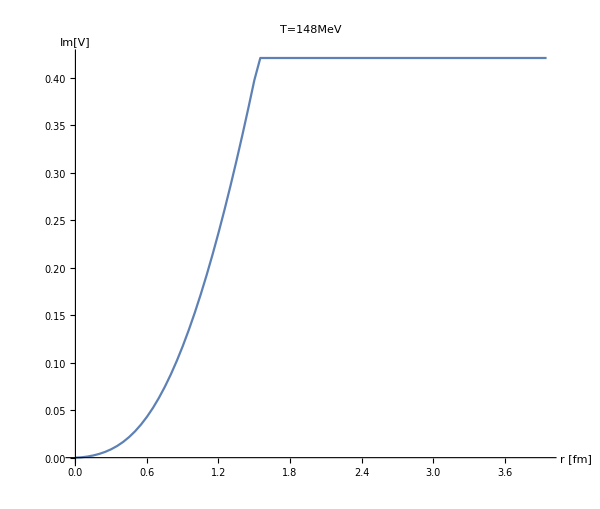

```mathematica
xsb=DiscretePlot[ImVsb[r/0.197,mdfitrandfinal[[3,1]],T0constfit[[1]][β[[3]]],T0constfit[[2]][β[[3]]],0.148],{r,1/1000,4,1/20},Filling->None,Joined->True,AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Im[V]"},PlotLabel->Style["T=148MeV",FontSize->25,FontFamily->"Helvetica",Black],ImageSize->{600,600}]
```

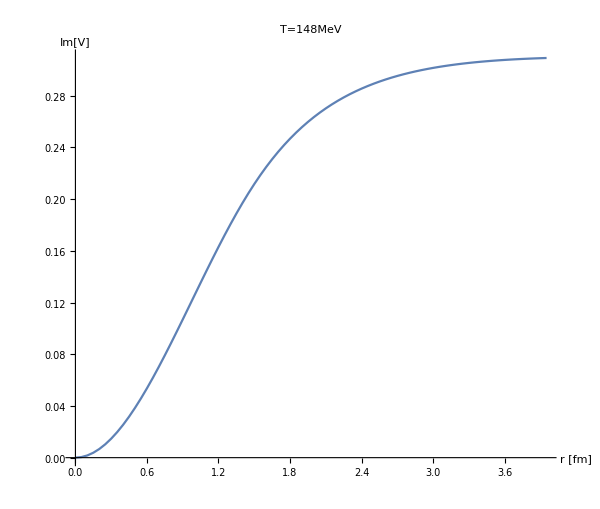

```mathematica
xI=DiscretePlot[ImVsI[r/0.197,rsb,mdfitrandfinal[[3,1]],T0constfit[[2]][β[[3]]],0.148],{r,1/1000,4,1/20},Filling->None,Joined->True,AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Im[V]"},PlotLabel->Style["T=148MeV",FontSize->25,FontFamily->"Helvetica",Black],ImageSize->{600,600}]
```

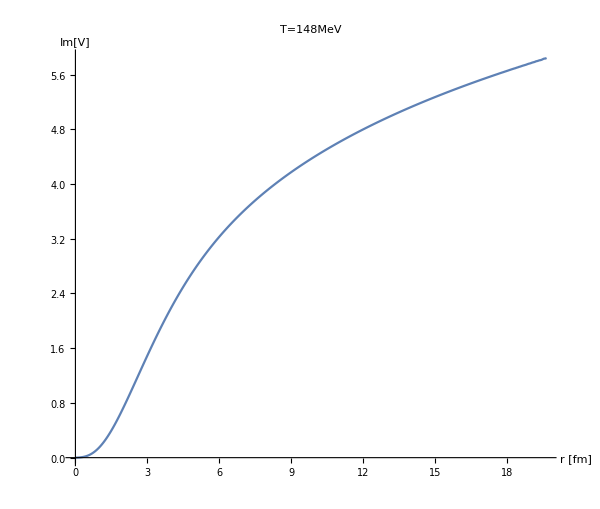

```mathematica
x=DiscretePlot[ImV[r/0.197,mdfitrandfinal[[3,1]],T0constfit[[1]][β[[3]]],T0constfit[[2]][β[[3]]],0.148],{r,1/1000,19.7,1/20},Filling->None,Joined->True,AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Im[V]"},PlotLabel->Style["T=148MeV",FontSize->25,FontFamily->"Helvetica",Black],ImageSize->{600,600}]
```

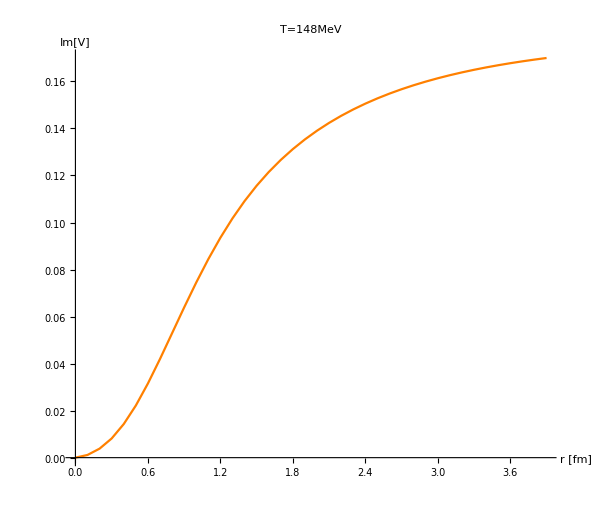

```mathematica
y=DiscretePlot[ImVold[r/0.197,mdfitrandfinal[[3,1]],T0constfit[[1]][β[[3]]],T0constfit[[2]][β[[3]]],0.148],{r,1/1000,4,1/10},Filling->None,Joined->True,PlotStyle->Orange,AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Im[V]"},PlotLabel->Style["T=148MeV",FontSize->25,FontFamily->"Helvetica",Black],ImageSize->{600,600},PlotRange->All]
```

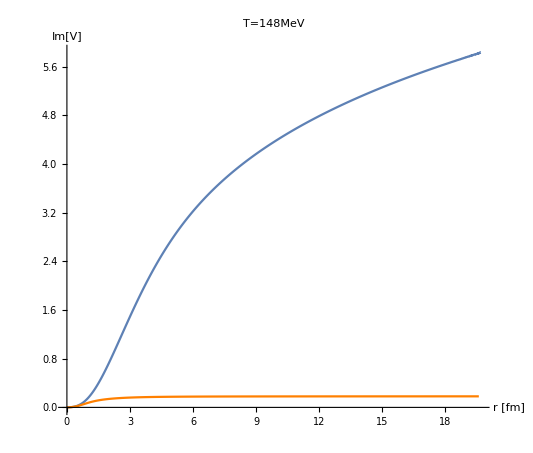

```mathematica
Show[x,y]
```

```mathematica
Show[xsb,y]
```

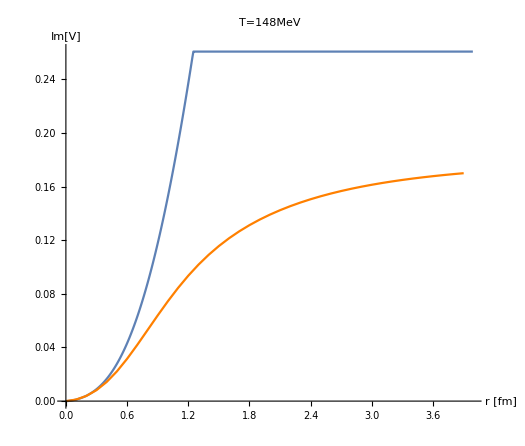

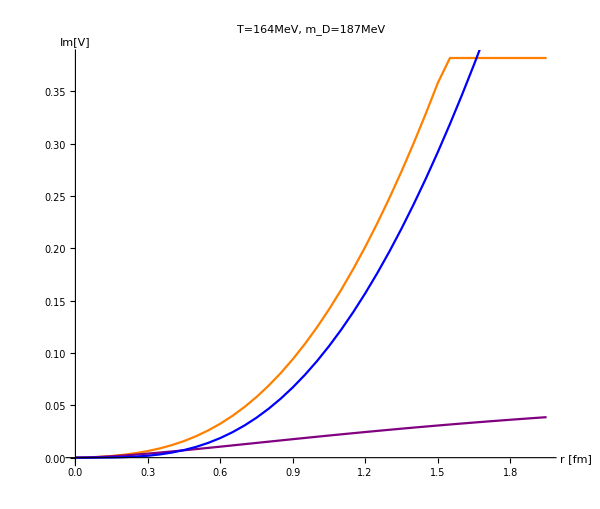

```mathematica
Block[{mD=mdfitrandfinal[[2,1]]},Show[DiscretePlot[ImVsb[r/0.197,mD,T0constfit[[1]][β[[2]]],T0constfit[[2]][β[[2]]],T[[2]]],{r,1/1000,2,1/20},Filling->None,Joined->True,PlotStyle->Orange,AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Im[V]"},PlotLabel->Style["T=164MeV, m_D=187MeV",FontSize->25,FontFamily->"Helvetica",Black],ImageSize->{600,600},PlotRange->All],DiscretePlot[ImVc[r/0.197,mD,T0constfit[[1]][β[[2]]],0.148],{r,1/1000,2,1/20},Filling->None,Joined->True,PlotStyle->Purple],DiscretePlot[ImVs[r/0.197,mD,T0constfit[[2]][β[[2]]],0.148],{r,1/1000,2,1/20},Filling->None,Joined->True,PlotStyle->Blue]]]
```

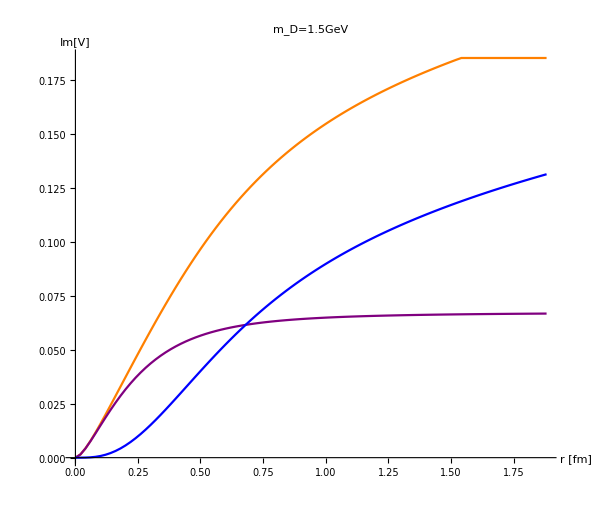

```mathematica
Block[{mD=1.5},Show[DiscretePlot[ImVsb[r/0.197,mD,T0constfit[[1]][β[[3]]],T0constfit[[2]][β[[3]]],0.148],{r,1/1000,1.9,1/50},Filling->None,Joined->True,PlotStyle->Orange,AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Im[V]"},PlotLabel->Style["m_D=1.5GeV",FontSize->25,FontFamily->"Helvetica",Black],ImageSize->{600,600},PlotRange->All],DiscretePlot[ImVc[r/0.197,mD,T0constfit[[1]][β[[3]]],0.148],{r,1/1000,1.9,1/50},Filling->None,Joined->True,PlotStyle->Purple],DiscretePlot[ImVs[r/0.197,mD,T0constfit[[2]][β[[3]]],0.148],{r,1/1000,1.9,1/50},Filling->None,Joined->True,PlotStyle->Blue]]]
```

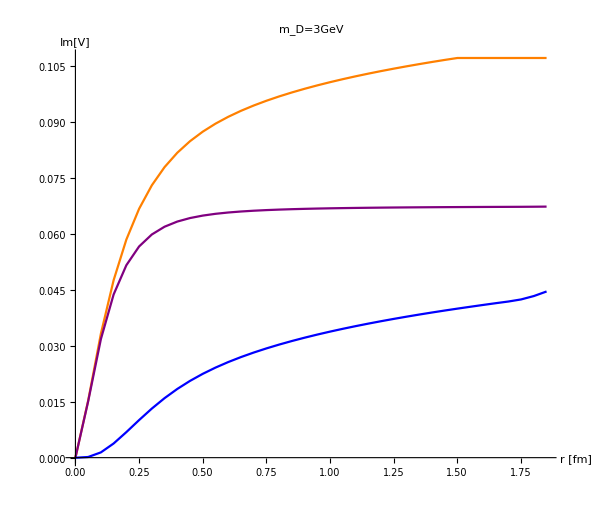

```mathematica
Block[{mD=3},Show[DiscretePlot[ImVsb[r/0.197,mD,T0constfit[[1]][β[[3]]],T0constfit[[2]][β[[3]]],0.148],{r,1/1000,1.9,1/20},Filling->None,Joined->True,PlotStyle->Orange,AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Im[V]"},PlotLabel->Style["m_D=3GeV",FontSize->25,FontFamily->"Helvetica",Black],ImageSize->{600,600},PlotRange->All],DiscretePlot[ImVc[r/0.197,mD,T0constfit[[1]][β[[3]]],0.148],{r,1/1000,1.9,1/20},Filling->None,Joined->True,PlotStyle->Purple],DiscretePlot[ImVs[r/0.197,mD,T0constfit[[2]][β[[3]]],0.148],{r,1/1000,1.9,1/20},Filling->None,Joined->True,PlotStyle->Blue]]]
```

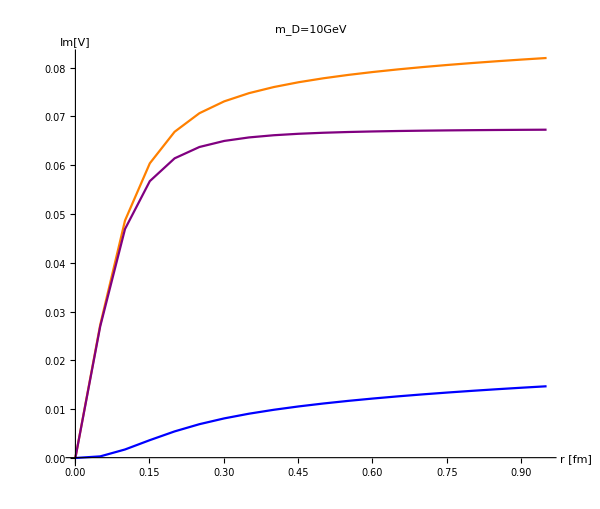

```mathematica
Block[{mD=5},Show[DiscretePlot[ImVsb[r/0.197,mD,T0constfit[[1]][β[[3]]],T0constfit[[2]][β[[3]]],0.148],{r,1/1000,1.,1/20},Filling->None,Joined->True,PlotStyle->Orange,AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Im[V]"},PlotLabel->Style["m_D=10GeV",FontSize->25,FontFamily->"Helvetica",Black],ImageSize->{600,600},PlotRange->All],DiscretePlot[ImVc[r/0.197,mD,T0constfit[[1]][β[[3]]],0.148],{r,1/1000,1.,1/20},Filling->None,Joined->True,PlotStyle->Purple],DiscretePlot[ImVs[r/0.197,mD,T0constfit[[2]][β[[3]]],0.148],{r,1/1000,1.,1/20},Filling->None,Joined->True,PlotStyle->Blue]]]
```

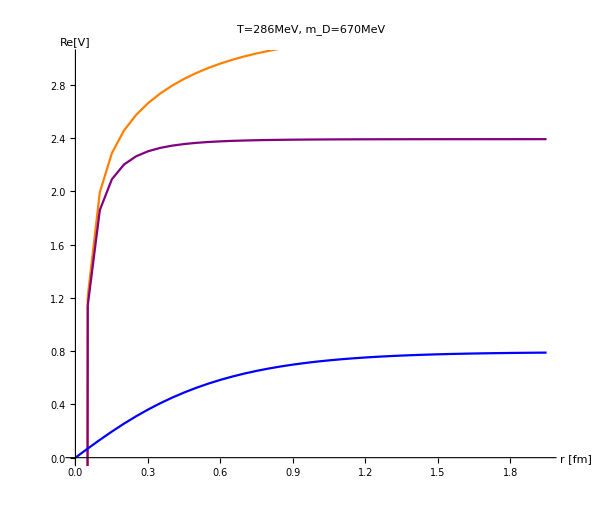

```mathematica
Block[{mD=mdfitrandfinal[[7,1]]},Show[DiscretePlot[ReVsb[r/0.197,mD,T0constfit[[1]][β[[7]]],T0constfit[[2]][β[[7]]],T0constfit[[3]][β[[7]]]],{r,1/1000,2,1/20},Filling->None,Joined->True,PlotStyle->Orange,AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Re[V]"},PlotLabel->Style["T=286MeV, m_D=670MeV",FontSize->25,FontFamily->"Helvetica",Black],ImageSize->{600,600},PlotRange->{0,3}],DiscretePlot[ReVc[r/0.197,mD,T0constfit[[1]][β[[7]]],T0constfit[[3]][β[[7]]]],{r,1/1000,2,1/20},Filling->None,Joined->True,PlotStyle->Purple],DiscretePlot[ReVs[r/0.197,mD,T0constfit[[2]][β[[7]]]],{r,1/1000,2,1/20},Filling->None,Joined->True,PlotStyle->Blue]]]
```

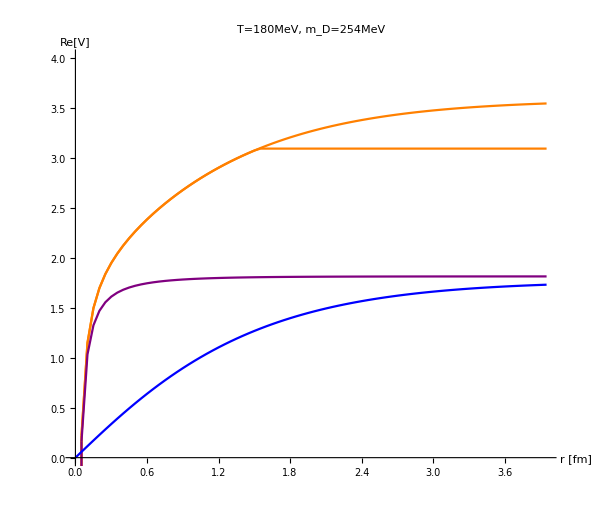

```mathematica
Block[{mD=mdfitrandfinal[[3,1]]},Show[DiscretePlot[{ReV[r/0.197,mD,T0constfit[[1]][β[[3]]],T0constfit[[2]][β[[3]]],T0constfit[[3]][β[[3]]]],ReVsb[r/0.197,mD,T0constfit[[1]][β[[3]]],T0constfit[[2]][β[[3]]],T0constfit[[3]][β[[3]]]]},{r,1/1000,4,1/20},Filling->None,Joined->True,PlotStyle->Orange,AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Re[V]"},PlotLabel->Style["T=180MeV, m_D=254MeV",FontSize->25,FontFamily->"Helvetica",Black],ImageSize->{600,600},PlotRange->{0,4}],DiscretePlot[ReVc[r/0.197,mD,T0constfit[[1]][β[[3]]],T0constfit[[3]][β[[3]]]],{r,1/1000,4,1/20},Filling->None,Joined->True,PlotStyle->Purple],DiscretePlot[ReVs[r/0.197,mD,T0constfit[[2]][β[[3]]]],{r,1/1000,4,1/20},Filling->None,Joined->True,PlotStyle->Blue]]]
```

## Combining into single figure

### Real Part

```mathematica
β1={6.9,7.48,6.8,6.9,7,7.125,7.25,7.3,7.48};
```

```mathematica
αcontβ1=Table[T0constfit[[1]][β1[[i]]],{i,1,Length[β1]}]
```

{0.471045,0.384542,0.485959,0.471045,0.456131,0.437488,0.418845,0.411388,0.384542}

```mathematica
σcontβ1=Table[T0constfit[[2]][β1[[i]]],{i,1,Length[β1]}]
```

{0.217066,0.264756,0.208843,0.217066,0.225288,0.235566,0.245844,0.249956,0.264756}

```mathematica
ccontβ1=Table[T0constfit[[3]][β1[[i]]],{i,1,Length[β1]}]
```

{1.7808,2.64753,1.63137,1.7808,1.93024,2.11703,2.30383,2.37854,2.64753}

```mathematica
TempP={"T=41MeV","T=72MeV","T=148MeV","T=164MeV","T=182MeV","T=205MeV","T=232MeV","T=243MeV","T=286MeV"};
```

```mathematica
TempP={"T=0.24T_C","T=0.42T_C","T=0.86T_C","T=0.95T_C","T=1.06T_C","T=1.19T_C","T=1.34T_C","T=1.41T_C","T=1.66T_C"};
```

```mathematica
TempP={"T≈0(β=6.9)","T≈0(β=7.48)","T=0.86T_C","T=0.95T_C","T=1.06T_C","T=1.19T_C","T=1.34T_C","T=1.41T_C","T=1.66T_C"};
```

```mathematica
For[l=1,l≤ 2,l++,PotReRescale[l]=T0data[[l]]/.{a_,b_,c_}:>{a,b-ccontβ1[[l]]-0.45*If[l==1,0,l]+6.,c}];
```

```mathematica
For[l=1,l≤ 5,l++,PotReRescale[l+2]=ReVdataTe[l]/.{a_,b_,c_}:>{a,b-ccontβ1[[l+2]]-0.45l+5.,c}];
```

```mathematica
For[l=6,l≤ 7,l++,PotReRescale[l+2]=ReVdataTe[l][[;;-14]]/.{a_,b_,c_}:>{a,b-ccontβ1[[l+2]]-0.45 l+5.,c}];
```

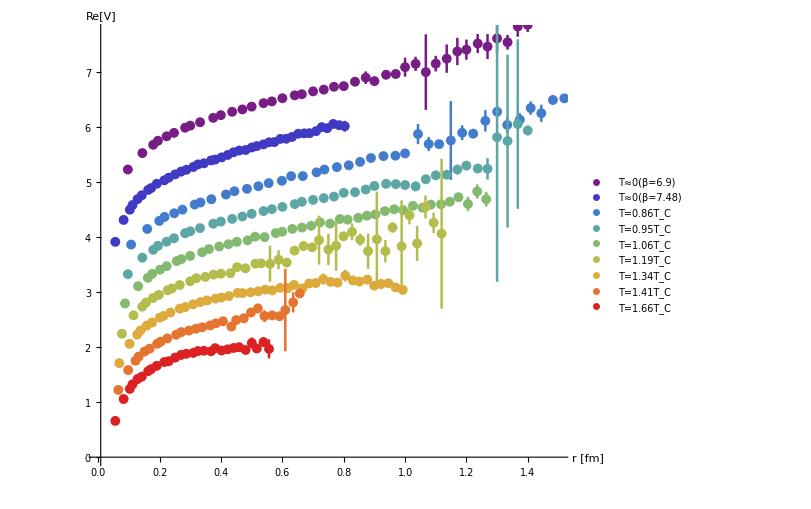

```mathematica
ReVdatPlot=ErrorListPlot[Table[PotReRescale[l],{l,1,9}],PlotRange->{{0.00001,1.5},{0.,7.7}},PlotStyle->Thread@{AbsolutePointSize[7.1],AbsoluteThickness[1.8],ColorData["Rainbow"]/@Range[0,1,1/8]},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},PlotLegends->Placed[PointLegend[TempP, LegendMarkerSize->8,LegendLayout->{"Row",3}],{0.66,0.12}],AspectRatio->0.85,AxesLabel->{"r [fm]","Re[V]"},ImageSize->{600,600}]
```

```mathematica
ReVplot=Join[Table[ReVm0[r/0.197327,αcontβ1[[l]],σcontβ1[[l]],ccontβ1[[l]]]-ccontβ1[[l]]-0.45*If[l==1,0,l]+6.,{l,1,2}],Table[ReV[r/0.197327,mdfitrandfinal[[l,1]],αcontβ1[[l+2]],σcontβ1[[l+2]],ccontβ1[[l+2]]]-ccontβ1[[l+2]]-0.45l+5.,{l,1,7}]];
```

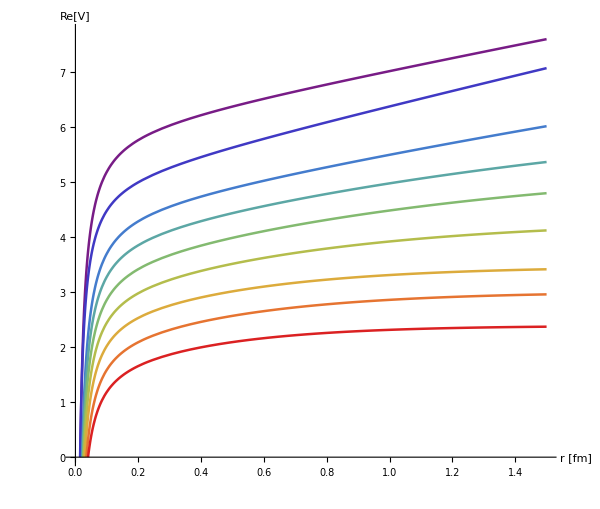

```mathematica
ReVanPlot=Plot[ReVplot,{r,0.001,1.5},PlotRange->{{0.00001,1.5},{0.,7.7}},PlotStyle->Thread@{AbsoluteThickness[1.8],ColorData["Rainbow"]/@Range[0,1,1/8]},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Re[V]"},ImageSize->{600,600},PlotRange->{{0,1.5},All}]
```

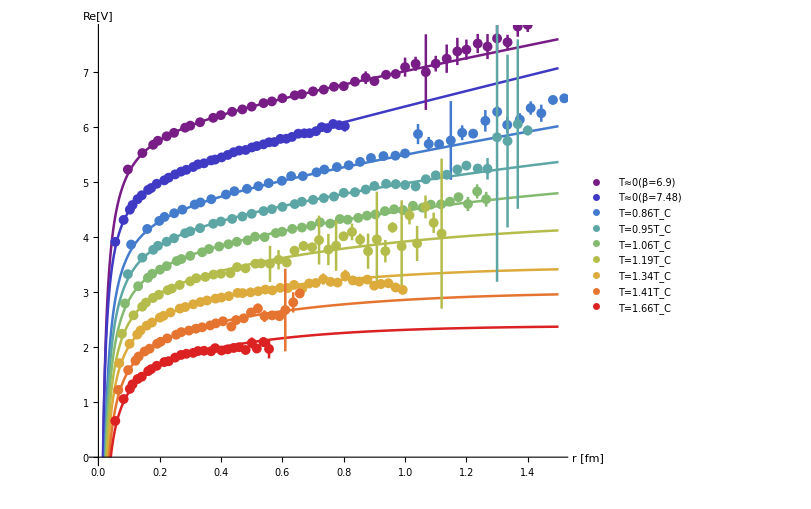

```mathematica
Show[{ReVanPlot,ReVdatPlot}]
```

```mathematica
αecontβ1=Table[T0errfit[[1]][β1[[i]]],{i,1,Length[β1]}]
```

{0.0470262,0.0268778,0.0505001,0.0470262,0.0435524,0.03921,0.0348677,0.0331307,0.0268778}

```mathematica
σecontβ1=Table[T0errfit[[2]][β1[[i]]],{i,1,Length[β1]}]
```

{0.0159167,0.0143866,0.0161805,0.0159167,0.0156529,0.0153231,0.0149933,0.0148614,0.0143866}

```mathematica
cecontβ1=Table[T0errfit[[3]][β1[[i]]],{i,1,Length[β1]}]
```

{0.0593392,0.0420462,0.0623207,0.0593392,0.0563576,0.0526307,0.0489037,0.047413,0.0420462}

```mathematica
ReVe[r_,l_,a_]:=ReVsb[r/0.197327,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],ccontβ1[[l+2]]]-ccontβ1[[l+2]]-0.45l+5.;
```

```mathematica
ReV0e[r_,l_,a_]:=ReVm0sb[r/0.197327,αcontβ1[[l]]-a αecontβ1[[l]],σcontβ1[[l]]+a σecontβ1[[l]],ccontβ1[[l]]+a cecontβ1[[l]]]-ccontβ1[[l]]-0.45*If[l==1,0,l]+6.;
```

```mathematica
TempP={"T=41MeV","T=72MeV","T=148MeV","T=164MeV","T=182MeV","T=205MeV","T=232MeV","T=243MeV","T=286MeV"};
```

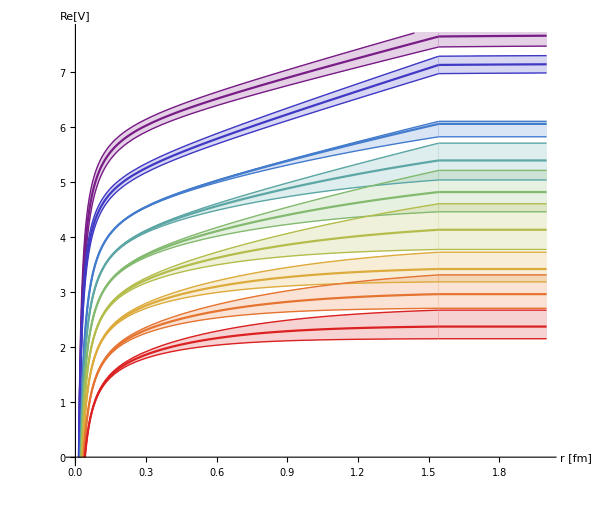

```mathematica
ReVanPlotError=Plot[{ReV0e[r,1,0],ReV0e[r,1,1],ReV0e[r,1,-1],ReV0e[r,2,0],ReV0e[r,2,1],ReV0e[r,2,-1],ReVe[r,1,0],ReVe[r,1,1],ReVe[r,1,-1],ReVe[r,2,0],ReVe[r,2,1],ReVe[r,2,-1],ReVe[r,3,0],ReVe[r,3,1],ReVe[r,3,-1],ReVe[r,4,0],ReVe[r,4,1],ReVe[r,4,-1],ReVe[r,5,0],ReVe[r,5,1],ReVe[r,5,-1],ReVe[r,6,0],ReVe[r,6,1],ReVe[r,6,-1],ReVe[r,7,0],ReVe[r,7,1],ReVe[r,7,-1]},{r,0.001,2},PlotRange->{{0.00001,2},{0.,7.7}},PlotStyle->{RGBColor[0.471412, 0.108766, 0.527016],{RGBColor[0.471412, 0.108766, 0.527016],Thin},{RGBColor[0.471412, 0.108766, 0.527016],Thin},RGBColor[0.250728, 0.225386, 0.769152],{RGBColor[0.250728, 0.225386, 0.769152],Thin},{RGBColor[0.250728, 0.225386, 0.769152],Thin},RGBColor[0.266122, 0.486664, 0.802529],{RGBColor[0.266122, 0.486664, 0.802529],Thin},{RGBColor[0.266122, 0.486664, 0.802529],Thin},RGBColor[0.36048, 0.655759, 0.645692],{RGBColor[0.36048, 0.655759, 0.645692],Thin},{RGBColor[0.36048, 0.655759, 0.645692],Thin},RGBColor[0.513417, 0.72992, 0.440682],{RGBColor[0.513417, 0.72992, 0.440682],Thin},{RGBColor[0.513417, 0.72992, 0.440682],Thin},RGBColor[0.705038, 0.742591, 0.299167],{RGBColor[0.705038, 0.742591, 0.299167],Thin},{RGBColor[0.705038, 0.742591, 0.299167],Thin},RGBColor[0.863512, 0.670771, 0.236564],{RGBColor[0.863512, 0.670771, 0.236564],Thin},{RGBColor[0.863512, 0.670771, 0.236564],Thin},RGBColor[0.902853, 0.453964, 0.192014],{RGBColor[0.902853, 0.453964, 0.192014],Thin},{RGBColor[0.902853, 0.453964, 0.192014],Thin},RGBColor[0.857359, 0.131106, 0.132128],{RGBColor[0.857359, 0.131106, 0.132128],Thin},{RGBColor[0.857359, 0.131106, 0.132128],Thin}},Filling->Flatten[Table[{i->{i+1},i->{i+2}},{i,1,27,3}]],AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Re[V]"},ImageSize->{600,600},PlotRange->{{0,1.5},All}]
```

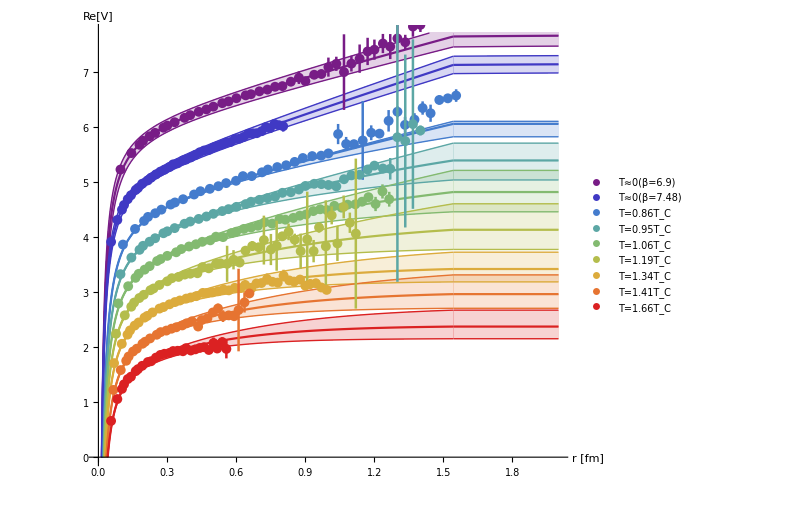

```mathematica
Show[{ReVanPlotError,ReVdatPlot}]
```

### Imag Part

```mathematica
Shift=1.
```

1.

```mathematica
For[l=1,l≤ 7,l++,PotImRescale[l]=ImVdataTe[l]/.{a_,b_,c_}:>{a-Shift*l+7*Shift,b,c}];
```

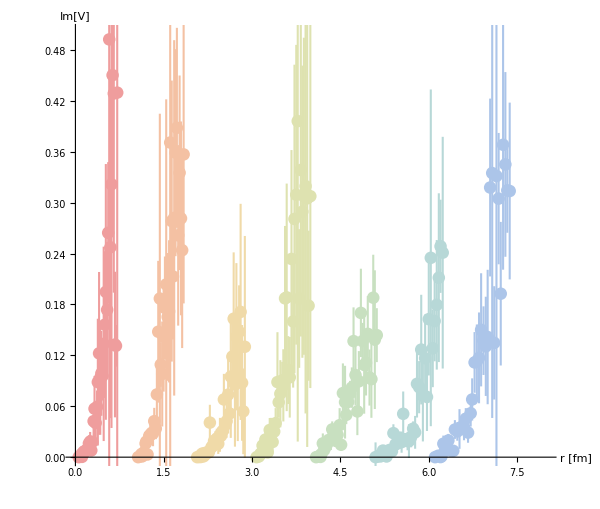

```mathematica
ImVdatPlot=ErrorListPlot[Table[PotImRescale[l][[1;;Floor[Length[PotImRescale[l]]*0.9]]],{l,1,7}],PlotRange->{{0,8},{0,0.5}},PlotStyle->Thread@{AbsolutePointSize[9],AbsoluteThickness[1.5],Lighter[Lighter[ColorData["Rainbow"]/@Range[2/8,1,1/8]]]},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->16},AspectRatio->0.85,PlotRange->{0,0.35},AxesLabel->{"r [fm]","Im[V]"},ImageSize->{600,600}]
```

```mathematica
ImVe[1,0]=Block[{l=1,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsb[r/0.197327,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,2,1/100}]];
ImVe[1,1]=Block[{l=1,a=1},ParallelTable[{r-Shift*l+7*Shift,ImVsb[r/0.197327,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,2,1/100}]];
ImVe[1,-1]=Block[{l=1,a=-1},ParallelTable[{r-Shift*l+7*Shift,ImVsb[r/0.197327,1/1000,αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,2,1/100}]];
ImVe[2,0]=Block[{l=2,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsb[r/0.197327,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,3,1/100}]];
ImVe[2,1]=Block[{l=2,a=1},ParallelTable[{r-Shift*l+7*Shift,ImVsb[r/0.197327,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,3,1/100}]];
ImVe[2,-1]=Block[{l=2,a=-1},ParallelTable[{r-Shift*l+7*Shift,ImVsb[r/0.197327,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,3,1/100}]];
ImVe[3,0]=Block[{l=3,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsb[r/0.197327,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,4,1/100}]];
ImVe[3,1]=Block[{l=3,a=1},ParallelTable[{r-Shift*l+7*Shift,ImVsb[r/0.197327,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,4,1/100}]];
ImVe[3,-1]=Block[{l=3,a=-1},ParallelTable[{r-Shift*l+7*Shift,ImVsb[r/0.197327,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,4,1/100}]];
ImVe[4,0]=Block[{l=4,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsb[r/0.197327,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,5,1/100}]];
ImVe[4,1]=Block[{l=4,a=1},ParallelTable[{r-Shift*l+7*Shift,ImVsb[r/0.197327,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,5,1/100}]];
ImVe[4,-1]=Block[{l=4,a=-1},ParallelTable[{r-Shift*l+7*Shift,ImVsb[r/0.197327,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,5,1/100}]];
ImVe[5,0]=Block[{l=5,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsb[r/0.197327,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,6,1/100}]];
ImVe[5,1]=Block[{l=5,a=1},ParallelTable[{r-Shift*l+7*Shift,ImVsb[r/0.197327,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,6,1/100}]];
ImVe[5,-1]=Block[{l=5,a=-1},ParallelTable[{r-Shift*l+7*Shift,ImVsb[r/0.197327,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,6,1/100}]];
ImVe[6,0]=Block[{l=6,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsb[r/0.197327,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,7,1/100}]];
ImVe[6,1]=Block[{l=6,a=1},ParallelTable[{r-Shift*l+7*Shift,ImVsb[r/0.197327,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,7,1/100}]];
ImVe[6,-1]=Block[{l=6,a=-1},ParallelTable[{r-Shift*l+7*Shift,ImVsb[r/0.197327,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,7,1/100}]];
ImVe[7,0]=Block[{l=7,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsb[r/0.197327,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,8,1/100}]];
ImVe[7,1]=Block[{l=7,a=1},ParallelTable[{r-Shift*l+7*Shift,ImVsb[r/0.197327,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,8,1/100}]];
ImVe[7,-1]=Block[{l=7,a=-1},ParallelTable[{r-Shift*l+7*Shift,ImVsb[r/0.197327,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,8,1/100}]];
```

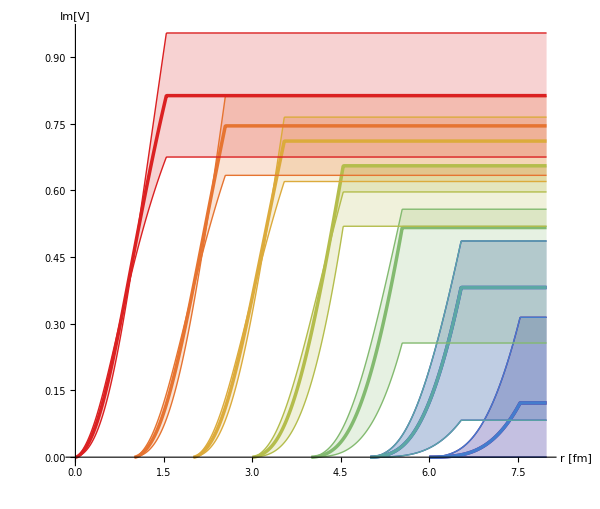

```mathematica
ImVPlotError=ListPlot[{ImVe[1,0],ImVe[1,1],ImVe[1,-1],ImVe[2,0],ImVe[2,1],ImVe[2,-1],ImVe[1,0],ImVe[1,1],ImVe[1,-1],ImVe[2,0],ImVe[2,1],ImVe[2,-1],ImVe[3,0],ImVe[3,1],ImVe[3,-1],ImVe[4,0],ImVe[4,1],ImVe[4,-1],ImVe[5,0],ImVe[5,1],ImVe[5,-1],ImVe[6,0],ImVe[6,1],ImVe[6,-1],ImVe[7,0],ImVe[7,1],ImVe[7,-1]},Joined->True,PlotStyle->{{RGBColor[0.471412, 0.108766, 0.527016],AbsoluteThickness[2.5]},{RGBColor[0.471412, 0.108766, 0.527016],Thin},{RGBColor[0.471412, 0.108766, 0.527016],Thin},{RGBColor[0.250728, 0.225386, 0.769152],AbsoluteThickness[2.5]},{RGBColor[0.250728, 0.225386, 0.769152],Thin},{RGBColor[0.250728, 0.225386, 0.769152],Thin},{RGBColor[0.266122, 0.486664, 0.802529],AbsoluteThickness[2.5]},{RGBColor[0.266122, 0.486664, 0.802529],Thin},{RGBColor[0.266122, 0.486664, 0.802529],Thin},{RGBColor[0.36048, 0.655759, 0.645692],AbsoluteThickness[2.5]},{RGBColor[0.36048, 0.655759, 0.645692],Thin},{RGBColor[0.36048, 0.655759, 0.645692],Thin},{RGBColor[0.513417, 0.72992, 0.440682],AbsoluteThickness[2.5]},{RGBColor[0.513417, 0.72992, 0.440682],Thin},{RGBColor[0.513417, 0.72992, 0.440682],Thin},{RGBColor[0.705038, 0.742591, 0.299167],AbsoluteThickness[2.5]},{RGBColor[0.705038, 0.742591, 0.299167],Thin},{RGBColor[0.705038, 0.742591, 0.299167],Thin},{RGBColor[0.863512, 0.670771, 0.236564],AbsoluteThickness[2.5]},{RGBColor[0.863512, 0.670771, 0.236564],Thin},{RGBColor[0.863512, 0.670771, 0.236564],Thin},{RGBColor[0.902853, 0.453964, 0.192014],AbsoluteThickness[2.5]},{RGBColor[0.902853, 0.453964, 0.192014],Thin},{RGBColor[0.902853, 0.453964, 0.192014],Thin},{RGBColor[0.857359, 0.131106, 0.132128],AbsoluteThickness[2.5]},{RGBColor[0.857359, 0.131106, 0.132128],Thin},{RGBColor[0.857359, 0.131106, 0.132128],Thin}},Filling->Flatten[Table[{i->{i+1},i->{i+2}},{i,1,27,3}]],AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Im[V]"},ImageSize->{600,600}]
```

```mathematica
Show[ImVdatPlot,ImVanPlotError]
```